```mathematica
f[x_]:=r* x + 4 x^3 - 9 x^5
fps=Solve[f[x]==0,x]//Flatten//Simplify
```

{x→0,x→-1/3 √(2-√(4+9 r)),x→1/3 √(2-√(4+9 r)),x→-1/3 √(2+√(4+9 r)),x→1/3 √(2+√(4+9 r))}

```mathematica
D[f[x],x]
```

r+12 x^2-45 x^4

```mathematica
(*Cecking the stability*)
D[f[x],x]/.fps[[1]] //Simplify

D[f[x],x]/.fps[[2]] //Flatten//Simplify
D[f[x],x]/.fps[[3]] //Flatten//Simplify
D[f[x],x]/.fps[[4]] //Flatten//Simplify
D[f[x],x]/.fps[[5]]//Flatten//Simplify
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[r].

Flatten[r]

4/9 (-4-9 r+2 √(4+9 r))

4/9 (-4-9 r+2 √(4+9 r))

-4/9 (4+9 r+2 √(4+9 r))

-4/9 (4+9 r+2 √(4+9 r))

```mathematica
Manipulate[Plot[r x + 4 x^3 - 9 x^5,{x,-1,1}],{r,-2,2}]
```

```mathematica
p2=StreamPlot[{-0.31 x + 4 x^3 - 9 x^5,0}, {x, -0.75, 0.75},{y,-0.02,0.02}];
```

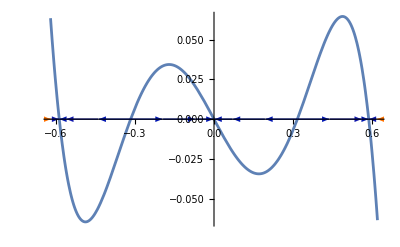

```mathematica
Show[p1,p2]
```

```mathematica
p3=Plot[{If[-1<=x<=0,fps[[1,2]],Indeterminate],If[0<=x<=1,fps[[1,2]],Indeterminate]},{x,-1,1},PlotStyle->{Blue,{Dashed,Red}}];
```

```mathematica
p3=Plot[{fps[[4,2]],fps[[2,2]],fps[[3,2]],fps[[5,2]]},{r,-1,1},PlotStyle->{Blue,
{Dashed,Red},{Dashed,Red},Blue,Blue},PlotLegends->{"Unstable" , "Stable"}];
```

```mathematica
Show[p3,p6,PlotRange->Full]
```

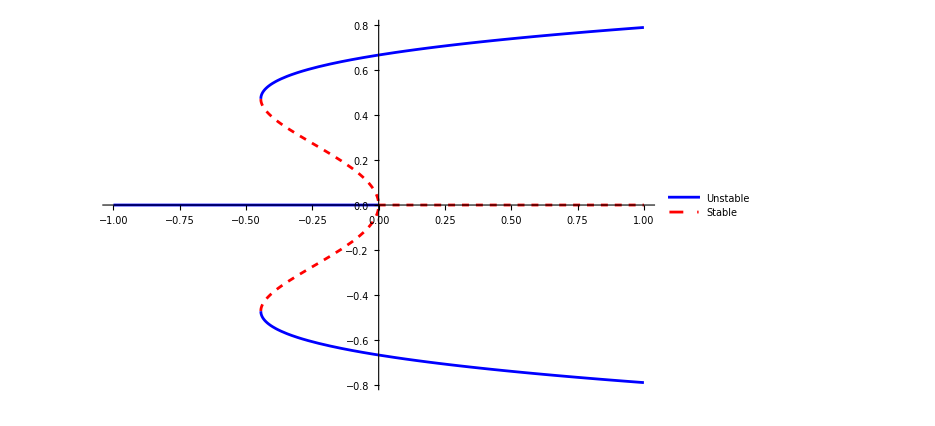

Find saddle-node bifurcations by finding the point when it changes from 3 to 5 fix points. This by finding at wich r the sum under de root is zeros in the

```mathematica
Solve[Sqrt[4+9r]==0]
```

{{r→-4/9}}